RPA for AlAs

Define anisotropy

```mathematica
EtaValue=5.79
```

5.79

OneoveraB, d: only appearing in tanh. Both in SI units (tanh then dimensionless, not relevant which units are used for energy)

```mathematica
oneoveraB=8636048389.489414
```

8.63605×10^9

```mathematica
d=100*10^(-9)
```

1/10000000

```mathematica
eps=10
```

10

```mathematica
rsn[nit_]=1/Sqrt[nit*10^(15)*Pi]*oneoveraB
```

154.078/(√nit)

```mathematica
Hplus[phi_,Eta_]=Sqrt[Sqrt[Eta]*Cos[phi]^2+1/Sqrt[Eta]*Sin[phi]^2]
```

√(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta))

```mathematica
Hminus[phi_,Eta_]=Sqrt[1/Sqrt[Eta]*Cos[phi]^2+Sqrt[Eta]*Sin[phi]^2]
```

√(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2)

```mathematica
Psi2[x_,y_]=x-Sqrt[(x+y*I)^2-1]
```

x-√(-1+(x+ⅈ y)^2)

```mathematica
fplus[y_,nu_,phi_,Eta_]=2*Re[Psi2[y/2.0*Hplus[phi,Eta],nu/Hplus[phi,Eta]]]/y
```

(2 Re[0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta))-√(-1+((ⅈ nu)/(√(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))+0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))^2)])/y

```mathematica
fminus[y_,nu_,phi_,Eta_]=2*Re[Psi2[y/2.0*Hminus[phi,Eta],nu/Hminus[phi,Eta]]]/y
```

(2 Re[0.5 y √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2)-√(-1+((ⅈ nu)/(√(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))+0.5 y √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))^2)])/y

```mathematica
vqchiSP[y_,phi_,nu_,rs_,Eta_, d1_]=-1.0/Sqrt[2]*rs*1/eps*Tanh[d1*Sqrt[2]/rs*oneoveraB*y](fplus[y,nu,phi,Eta]/(y*Hplus[phi,Eta])+fminus[y,nu,phi,Eta]/(y*Hminus[phi,Eta]))
```

-0.0707107 rs ((2 Re[0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta))-√(-1+((ⅈ nu)/(√(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))+0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))^2)])/(y^2 √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))+(2 Re[0.5 y √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2)-√(-1+((ⅈ nu)/(√(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))+0.5 y √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))^2)])/(y^2 √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))) Tanh[(1.22132×10^10 d1 y)/rs]

```mathematica
vqchiVP[y_,phi_,nu_,rs_,Eta_,d1_]=-Sqrt[2]*rs*1/eps*Tanh[d1*Sqrt[2]/rs*oneoveraB*y]*(fplus[y,nu,phi,Eta]/(y*Hplus[phi,Eta]))
```

-(√2 rs Re[0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta))-√(-1+((ⅈ nu)/(√(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))+0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))^2)] Tanh[(1.22132×10^10 d1 y)/rs])/(5 y^2 √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))

```mathematica
vqchiSVP[y_,phi_,nu_,rs_,Eta_,d1_]=-0.5*rs*1/eps*Tanh[d1*2/rs*oneoveraB*y]*(fplus[y,nu,phi,Eta]/(y*Hplus[phi,Eta]))
```

-(0.1 rs Re[0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta))-√(-1+((ⅈ nu)/(√(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))+0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))^2)] Tanh[(1.72721×10^10 d1 y)/rs])/(y^2 √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))

```mathematica
vqchisym[y_,phi_,nu_,rs_,Eta_,d1_]=-2*rs*1/eps*Tanh[d1*1.0/rs*oneoveraB*y]*(fplus[y,nu,phi,Eta]/(y*Hplus[phi,Eta])+fminus[y,nu,phi,Eta]/(y*Hminus[phi,Eta]))
```

-1/5 rs ((2 Re[0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta))-√(-1+((ⅈ nu)/(√(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))+0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))^2)])/(y^2 √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))+(2 Re[0.5 y √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2)-√(-1+((ⅈ nu)/(√(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))+0.5 y √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))^2)])/(y^2 √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))) Tanh[(8.63605×10^9 d1 y)/rs]

```mathematica
encorSPscreened[y_,phi_,nu_,rs_,Eta_,d1_]=2/(Pi*rs^2*2*Pi)*y^2*(vqchiSP[y,phi,nu,rs,Eta,d1]+Log[1-vqchiSP[y,phi,nu,rs,Eta,d1]])
```

1/(π^2 rs^2)y^2 (Log[1+0.0707107 rs ((2 Re[0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta))-√(-1+((ⅈ nu)/(√(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))+0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))^2)])/(y^2 √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))+(2 Re[0.5 y √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2)-√(-1+((ⅈ nu)/(√(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))+0.5 y √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))^2)])/(y^2 √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))) Tanh[(1.22132×10^10 d1 y)/rs]]-0.0707107 rs ((2 Re[0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta))-√(-1+((ⅈ nu)/(√(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))+0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))^2)])/(y^2 √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))+(2 Re[0.5 y √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2)-√(-1+((ⅈ nu)/(√(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))+0.5 y √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))^2)])/(y^2 √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))) Tanh[(1.22132×10^10 d1 y)/rs])

```mathematica
encorVPscreened[y_,phi_,nu_,rs_,Eta_,d1_]=2/(Pi*rs^2*2*Pi)*y^2*(vqchiVP[y,phi,nu,rs,Eta,d1]+Log[1-vqchiVP[y,phi,nu,rs,Eta,d1]])
```

1/(π^2 rs^2)y^2 (Log[1+(√2 rs Re[0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta))-√(-1+((ⅈ nu)/(√(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))+0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))^2)] Tanh[(1.22132×10^10 d1 y)/rs])/(5 y^2 √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))]-(√2 rs Re[0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta))-√(-1+((ⅈ nu)/(√(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))+0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))^2)] Tanh[(1.22132×10^10 d1 y)/rs])/(5 y^2 √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta))))

```mathematica
encorSVPscreened[y_,phi_,nu_,rs_,Eta_,d1_]=8/(Pi*rs^2*2*Pi)*y^2*(vqchiSVP[y,phi,nu,rs,Eta,d1]+Log[1-vqchiSVP[y,phi,nu,rs,Eta,d1]])
```

1/(π^2 rs^2)4 y^2 (Log[1+(0.1 rs Re[0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta))-√(-1+((ⅈ nu)/(√(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))+0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))^2)] Tanh[(1.72721×10^10 d1 y)/rs])/(y^2 √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))]-(0.1 rs Re[0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta))-√(-1+((ⅈ nu)/(√(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))+0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))^2)] Tanh[(1.72721×10^10 d1 y)/rs])/(y^2 √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta))))

```mathematica
encorsymscreened[y_,phi_,nu_,rs_,Eta_,d1_]=1/(2*Pi*rs^2*2*Pi)*y^2*(vqchisym[y,phi,nu,rs,Eta,d1]+Log[1-vqchisym[y,phi,nu,rs,Eta,d1]])
```

1/(4 π^2 rs^2)y^2 (Log[1+1/5 rs ((2 Re[0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta))-√(-1+((ⅈ nu)/(√(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))+0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))^2)])/(y^2 √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))+(2 Re[0.5 y √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2)-√(-1+((ⅈ nu)/(√(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))+0.5 y √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))^2)])/(y^2 √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))) Tanh[(8.63605×10^9 d1 y)/rs]]-1/5 rs ((2 Re[0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta))-√(-1+((ⅈ nu)/(√(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))+0.5 y √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))^2)])/(y^2 √(√Eta Cos[phi]^2+Sin[phi]^2/(√Eta)))+(2 Re[0.5 y √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2)-√(-1+((ⅈ nu)/(√(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))+0.5 y √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))^2)])/(y^2 √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))) Tanh[(8.63605×10^9 d1 y)/rs])

```mathematica
num=200
```

200

```mathematica
1.0/num*Sum[NIntegrate[2*Pi*encorVPscreened[y,2*Pi/num*i,nu, 15, EtaValue,d],{y,0.0001,500},{nu,0.0001,500}],{i,num}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

-0.0034443+0. ⅈ

```mathematica
1.0/num*Sum[NIntegrate[2*Pi*encorSPscreened[y,2*Pi/num*i,nu, 15, EtaValue,d],{y,0.0001,500},{nu,0.0001,500}],{i,num}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

-0.00325602+0. ⅈ

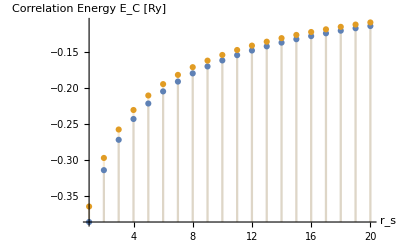

```mathematica
DiscretePlot[{1.0/num*Sum[NIntegrate[2*Pi*encorVPscreened[y,2*Pi/num*i,nu, rs,EtaValue],{y,0.0001,100},{nu,0.0001,100}],{i,num}], 1.0/num*Sum[NIntegrate[2*Pi*encorSPscreened[y,2*Pi/num*i,nu, rs,EtaValue],{y,0.0001,100},{nu,0.0001,100}],{i,num}]},{rs,1,20},AxesLabel->{"r_s","Correlation Energy E_C [Ry]"},PlotLabels->{"VP","SP"}]
```

Kinetic energy for symmetric state

```mathematica
Ekinsym[rs_]=1/(2*rs^2)
```

1/(2 rs^2)

Kinetic energy for spin-polarized state

```mathematica
EkinSP[rs_]=1/(rs^2)
```

1/rs^2

Kinetic energy for valley-polarized state

```mathematica
EkinVP[rs_]=1/(rs^2)
```

1/rs^2

Kinetic energy for spin-valley-polarized state

```mathematica
EkinSVP[rs_]=2*1/(rs^2)
```

2/rs^2

Exchange energy - need factor from phi integration (factor 2 after for 8 vs 4 - need to check!!)

```mathematica
phiintegration[phi_,eta_]=1/Sqrt[eta^(-1/2)*Cos[phi]^2+eta^(1/2)*Sin[phi]^2]
```

1/(√(Cos[phi]^2/(√eta)+√eta Sin[phi]^2))

```mathematica
phifactor[Eta_]=NIntegrate[phiintegration[phi,Eta],{phi,0,2*Pi}]/(2*Pi)
```

NIntegrate::inumr: The integrand 1/(√(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

NIntegrate[phiintegration[phi,Eta],{phi,0,2 π}]/(2 π)

```mathematica
qrev[phi_,Eta_]=Sqrt[Eta^(-1/2)*Cos[phi]^2+Eta^(1/2)*Sin[phi]^2]
```

√(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2)

Exchange energy for symmetric state

```mathematica
Exsymscreened[z_,phi_,Eta_,rs_,d1_]=-2/rs*1/eps*Tanh[2*z*d1*oneoveraB*1/rs*qrev[phi,Eta]]/qrev[phi,Eta]*(1-2/Pi*(ArcSin[z]+z*Sqrt[1-z^2]))/(2*Pi)
```

-((1-(2 (z √(1-z^2)+ArcSin[z]))/π) Tanh[(1.72721×10^10 d1 z √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))/rs])/(10 π rs √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))

Exchange energy for spin-polarized state

```mathematica
ExSPscreened[z_,phi_,Eta_,rs_,d1_]=-2*Sqrt[2]/rs*1/eps*Tanh[2*z*d1*oneoveraB*Sqrt[2]/rs*qrev[phi,Eta]]/qrev[phi,Eta]*(1-2/Pi*(ArcSin[z]+z*Sqrt[1-z^2]))/(2*Pi)
```

-((1-(2 (z √(1-z^2)+ArcSin[z]))/π) Tanh[(2.44264×10^10 d1 z √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))/rs])/(5 √2 π rs √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))

```mathematica
ExSPcompare[z_,phi_,Eta_,rs_,d1_]=-2*Sqrt[2]/rs*1/eps*Tanh[2*z*d1/rs*qrev[phi,Eta]]/qrev[phi,Eta]*(1-2/Pi*(ArcSin[z]+z*Sqrt[1-z^2]))/(2*Pi)
```

-((1-(2 (z √(1-z^2)+ArcSin[z]))/π) Tanh[(2 d1 z √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))/rs])/(5 √2 π rs √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))

```mathematica
NIntegrate[ExSPscreened[z,phi,EtaValue,15,d],{z,0,1},{phi,0,2*Pi}]
```

-0.00755356

Exchange energy for valley-polarized state

```mathematica
ExVPscreened[z_,phi_,Eta_,rs_,d1_]=-2*Sqrt[2]/rs*1/eps*Tanh[2*z*d1*oneoveraB*Sqrt[2]/rs*qrev[phi,Eta]]/qrev[phi,Eta]*(1-2/Pi*(ArcSin[z]+z*Sqrt[1-z^2]))/(2*Pi)
```

-((1-(2 (z √(1-z^2)+ArcSin[z]))/π) Tanh[(2.44264×10^10 d1 z √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))/rs])/(5 √2 π rs √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))

Exchange energy for spin-valley polarized state

```mathematica
ExSVPscreened[z_,phi_,Eta_,rs_,d1_]=-4/rs*1/eps*Tanh[2*z*d1*oneoveraB*2/rs*qrev[phi,Eta]]/qrev[phi,Eta]*(1-2/Pi*(ArcSin[z]+z*Sqrt[1-z^2]))/(2*Pi)
```

-((1-(2 (z √(1-z^2)+ArcSin[z]))/π) Tanh[(3.45442×10^10 d1 z √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))/rs])/(5 π rs √(Cos[phi]^2/(√Eta)+√Eta Sin[phi]^2))

```mathematica
DiscretePlot[{EkinVP[rs]-Ekinsym[rs]+NIntegrate[ExVPscreened[z,phi,EtaValue,rs,d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValue,rs,d],{z,0,1},{phi,0,2*Pi}]+1.0/num*Sum[NIntegrate[2*Pi*(encorVPscreened[y,2*Pi/num*i,nu, rs, EtaValue,d]-encorsymscreened[y,2*Pi/num*i,nu, rs, EtaValue,d]),{y,0.0001,100},{nu,0.0001,100}],{i,num}], EkinSP[rs]-Ekinsym[rs]+NIntegrate[ExSPscreened[z,phi,EtaValue,rs,d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValue,rs,d],{z,0,1},{phi,0,2*Pi}]+1.0/num*Sum[NIntegrate[2*Pi*(encorSPscreened[y,2*Pi/num*i,nu, rs, EtaValue,d]-encorsymscreened[y,2*Pi/num*i,nu, rs, EtaValue,d]),{y,0.0001,100},{nu,0.0001,100}],{i,num}],EkinSVP[rs]-Ekinsym[rs]+NIntegrate[ExSVPscreened[z,phi,EtaValue,rs,d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValue,rs,d],{z,0,1},{phi,0,2*Pi}]+1.0/num*Sum[NIntegrate[2*Pi*(encorSVPscreened[y,2*Pi/num*i,nu, rs, EtaValue,d]-encorsymscreened[y,2*Pi/num*i,nu, rs, EtaValue,d]),{y,0.0001,100},{nu,0.0001,100}],{i,num}] },{rs,1500,6000,1000},AxesLabel->{"r_s","E_RPA-Esym_RPA"},PlotLabels->{"VP","SP", "SVP"}]
```

-Graphics-

```mathematica
DiscretePlot[{EkinVP[rs]-Ekinsym[rs]+NIntegrate[ExVPscreened[z,phi,EtaValue,rs,d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValue,rs,d],{z,0,1},{phi,0,2*Pi}]+1.0/num*Sum[NIntegrate[2*Pi*(encorVPscreened[y,2*Pi/num*i,nu, rs, EtaValue,d]-encorsymscreened[y,2*Pi/num*i,nu, rs, EtaValue,d]),{y,0.0001,100},{nu,0.0001,100}],{i,num}], EkinSP[rs]-Ekinsym[rs]+NIntegrate[ExSPscreened[z,phi,EtaValue,rs,d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValue,rs,d],{z,0,1},{phi,0,2*Pi}]+1.0/num*Sum[NIntegrate[2*Pi*(encorSPscreened[y,2*Pi/num*i,nu, rs, EtaValue,d]-encorsymscreened[y,2*Pi/num*i,nu, rs, EtaValue,d]),{y,0.0001,100},{nu,0.0001,100}],{i,num}],EkinSVP[rs]-Ekinsym[rs]+NIntegrate[ExSVPscreened[z,phi,EtaValue,rs,d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValue,rs,d],{z,0,1},{phi,0,2*Pi}]+1.0/num*Sum[NIntegrate[2*Pi*(encorSVPscreened[y,2*Pi/num*i,nu, rs, EtaValue,d]-encorsymscreened[y,2*Pi/num*i,nu, rs, EtaValue,d]),{y,0.0001,100},{nu,0.0001,100}],{i,num}] },{rs,10,200,10},AxesLabel->{"r_s","E_RPA-Esym_RPA"},PlotLabels->{"VP","SP", "SVP"}]
```

-Graphics-

```mathematica
rsn[1]
```

154.078

```mathematica
DiscretePlot[{EkinVP[rs]-Ekinsym[rs]+NIntegrate[ExVPscreened[z,phi,EtaValue,rs,d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValue,rs,d],{z,0,1},{phi,0,2*Pi}]+1.0/num*Sum[NIntegrate[2*Pi*(encorVPscreened[y,2*Pi/num*i,nu, rs, EtaValue,d]-encorsymscreened[y,2*Pi/num*i,nu, rs, EtaValue,d]),{y,0.0001,100},{nu,0.0001,100}],{i,num}], EkinSP[rs]-Ekinsym[rs]+NIntegrate[ExSPscreened[z,phi,EtaValue,rs,d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValue,rs,d],{z,0,1},{phi,0,2*Pi}]+1.0/num*Sum[NIntegrate[2*Pi*(encorSPscreened[y,2*Pi/num*i,nu, rs, EtaValue,d]-encorsymscreened[y,2*Pi/num*i,nu, rs, EtaValue,d]),{y,0.0001,100},{nu,0.0001,100}],{i,num}] },{rs,10,200,10},AxesLabel->{"r_s","E_RPA-Esym_RPA"},PlotLabels->{"VP","SP"}]
```

-Graphics-

```mathematica
DiscretePlot[{EkinVP[rsn[nit]]-Ekinsym[rsn[nit]]+NIntegrate[ExVPscreened[z,phi,EtaValue,rsn[nit],d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValue,rsn[nit],d],{z,0,1},{phi,0,2*Pi}]+1.0/num*Sum[NIntegrate[2*Pi*(encorVPscreened[y,2*Pi/num*i,nu, rsn[nit], EtaValue,d]-encorsymscreened[y,2*Pi/num*i,nu, rsn[nit], EtaValue,d]),{y,0.0001,100},{nu,0.0001,100}],{i,num}], EkinSP[rsn[nit]]-Ekinsym[rsn[nit]]+NIntegrate[ExSPscreened[z,phi,EtaValue,rsn[nit],d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValue,rsn[nit],d],{z,0,1},{phi,0,2*Pi}]+1.0/num*Sum[NIntegrate[2*Pi*(encorSPscreened[y,2*Pi/num*i,nu, rsn[nit], EtaValue,d]-encorsymscreened[y,2*Pi/num*i,nu, rsn[nit], EtaValue,d]),{y,0.0001,100},{nu,0.0001,100}],{i,num}],EkinSVP[rsn[nit]]-Ekinsym[rsn[nit]]+NIntegrate[ExSVPscreened[z,phi,EtaValue,rsn[nit],d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValue,rsn[nit],d],{z,0,1},{phi,0,2*Pi}]+1.0/num*Sum[NIntegrate[2*Pi*(encorSVPscreened[y,2*Pi/num*i,nu, rsn[nit], EtaValue,d]-encorsymscreened[y,2*Pi/num*i,nu, rsn[nit], EtaValue,d]),{y,0.0001,100},{nu,0.0001,100}],{i,num}] },{nit,1,50,5},AxesLabel->{"n in 10^(11) cm-2","E_RPA-Esym_RPA"},PlotLabels->{"VP","SP", "SVP"}]
```

-Graphics-

```mathematica
DiscretePlot[{EkinVP[rsn[nit]]-Ekinsym[rsn[nit]]+NIntegrate[ExVPscreened[z,phi,EtaValue,rsn[nit],d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValue,rsn[nit],d],{z,0,1},{phi,0,2*Pi}]+1.0/num*Sum[NIntegrate[2*Pi*(encorVPscreened[y,2*Pi/num*i,nu, rsn[nit], EtaValue,d]-encorsymscreened[y,2*Pi/num*i,nu, rsn[nit], EtaValue,d]),{y,0.0001,100},{nu,0.0001,100}],{i,num}], EkinSP[rsn[nit]]-Ekinsym[rsn[nit]]+NIntegrate[ExSPscreened[z,phi,EtaValue,rsn[nit],d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValue,rsn[nit],d],{z,0,1},{phi,0,2*Pi}]+1.0/num*Sum[NIntegrate[2*Pi*(encorSPscreened[y,2*Pi/num*i,nu, rsn[nit], EtaValue,d]-encorsymscreened[y,2*Pi/num*i,nu, rsn[nit], EtaValue,d]),{y,0.0001,100},{nu,0.0001,100}],{i,num}]},{nit,10,50,2},AxesLabel->{"n in 10^(11) cm-2","E_RPA-Esym_RPA"},PlotLabels->{"VP","SP", "SVP"}]
```

-Graphics-

Vary Eta

```mathematica
EtaValueSmaller=2.5
```

2.5

```mathematica
DiscretePlot[{EkinVP[rsn[nit]]-Ekinsym[rsn[nit]]+NIntegrate[ExVPscreened[z,phi,EtaValueSmaller,rsn[nit],d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValueSmaller,rsn[nit],d],{z,0,1},{phi,0,2*Pi}]+1.0/num*Sum[NIntegrate[2*Pi*(encorVPscreened[y,2*Pi/num*i,nu, rsn[nit], EtaValueSmaller,d]-encorsymscreened[y,2*Pi/num*i,nu, rsn[nit], EtaValueSmaller,d]),{y,0.0001,100},{nu,0.0001,100}],{i,num}], EkinSP[rsn[nit]]-Ekinsym[rsn[nit]]+NIntegrate[ExSPscreened[z,phi,EtaValueSmaller,rsn[nit],d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValueSmaller,rsn[nit],d],{z,0,1},{phi,0,2*Pi}]+1.0/num*Sum[NIntegrate[2*Pi*(encorSPscreened[y,2*Pi/num*i,nu, rsn[nit], EtaValueSmaller,d]-encorsymscreened[y,2*Pi/num*i,nu, rsn[nit], EtaValueSmaller,d]),{y,0.0001,100},{nu,0.0001,100}],{i,num}],EkinSVP[rsn[nit]]-Ekinsym[rsn[nit]]+NIntegrate[ExSVPscreened[z,phi,EtaValueSmaller,rsn[nit],d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValueSmaller,rsn[nit],d],{z,0,1},{phi,0,2*Pi}]+1.0/num*Sum[NIntegrate[2*Pi*(encorSVPscreened[y,2*Pi/num*i,nu, rsn[nit], EtaValueSmaller]-encorsymscreened[y,2*Pi/num*i,nu, rsn[nit], EtaValueSmaller]),{y,0.0001,100},{nu,0.0001,100}],{i,num}] },{nit,0.001,0.01,0.001},AxesLabel->{"n in 10^(11) cm-2","E_RPA-Esym_RPA"},PlotLabels->{"VP","SP", "SVP"}]
```

NIntegrate::inumr: The integrand 2 π (encorSVPscreened[y,(i π)/100,nu,154.078/(√nit),2.5]-encorsymscreened[y,(i π)/100,nu,154.078/(√nit),2.5]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.0001,100},{0.0001,100}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

Comparison with only Ekin+Ex (withou
t correlation energy)

```mathematica
DiscretePlot[{EkinVP[rsn[nit]]-Ekinsym[rsn[nit]]+NIntegrate[ExVPscreened[z,phi,EtaValue,rsn[nit],d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValue,rsn[nit],d],{z,0,1},{phi,0,2*Pi}], EkinSP[rsn[nit]]-Ekinsym[rsn[nit]]+NIntegrate[ExSPscreened[z,phi,EtaValue,rsn[nit],d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValue,rsn[nit],d],{z,0,1},{phi,0,2*Pi}],EkinSVP[rsn[nit]]-Ekinsym[rsn[nit]]+NIntegrate[ExSVPscreened[z,phi,EtaValue,rsn[nit],d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValue,rsn[nit],d],{z,0,1},{phi,0,2*Pi}] },{nit,1,200,10},AxesLabel->{"n in 10^(11) cm-2","E_RPA-Esym_RPA"},PlotLabels->{"VP","SP", "SVP"}]
```

-Graphics-

```mathematica
EkinSP[rsn[200]]*oneoveraB/2*(1.60217663*10^(-19))^2/(4*Pi*8.8541878128*10^(-12))
```

8.39261×10^-21

```mathematica
d2=100*10^(-9)*Sqrt[2]*oneoveraB
```

1221.32

```mathematica
NIntegrate[ExSPcompare[z,phi,1,rsn[100],d2],{z,0,1},{phi,0,2*Pi}]*oneoveraB/2*(1.60217634*10^(-19))^2/(4*Pi*8.8541878128*10^(-12))
```

-7.68184×10^-21

```mathematica
NIntegrate[ExVPscreened[z,phi,1,rsn[100],d],{z,0,1},{phi,0,2*Pi}]*oneoveraB/2*(1.60217634*10^(-19))^2/(4*Pi*8.8541878128*10^(-12))
```

-7.68184×10^-21

```mathematica
NIntegrate[ExSPscreened[z,phi,1,rsn[100],d],{z,0,1},{phi,0,2*Pi}]
```

-0.00771113

-0.0779101

```mathematica
NIntegrate[ExVPscreened[z,phi,1,rsn[1],d],{z,0,1},{phi,0,2*Pi}]*oneoveraB/2*(1.60217634*10^(-19))^2/(4*Pi*8.8541878128*10^(-12))
```

-6.9999×10^-22

```mathematica
EkinVP[rsn[1]]*oneoveraB/2*(1.60217663*10^(-19))^2/(4*Pi*8.8541878128*10^(-12))
```

4.1963×10^-23

```mathematica
num=200
```

200

```mathematica
1.0/num*Sum[NIntegrate[2*Pi*(encorVPscreened[y,2*Pi/num*i,nu, rsn[1], 1,d]),{y,0.0001,100},{nu,0.0001,100}],{i,num}]*oneoveraB/2*(1.60217663*10^(-19))^2/(4*Pi*8.8541878128*10^(-12))
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

-1.35202×10^-21+0. ⅈ

```mathematica
Anisotropy of Fermi Surface within HF
```

```mathematica
EtaRatio[Eta_,Etatilde_]=((Eta/Etatilde)^(0.5)+(Eta/Etatilde)^(-0.5))/2.0
```

0.5 (1/(Eta/Etatilde)^0.5+(Eta/Etatilde)^0.5)

```mathematica
EtaRatio[5,5]
```

1.

```mathematica
EkinVPEta[rs_, Eta_, Etatilde_]=EkinVP[rs]*EtaRatio[Eta,Etatilde]
```

(0.5 (1/(Eta/Etatilde)^0.5+(Eta/Etatilde)^0.5))/rs^2

```mathematica
EkinSPEta[rs_, Eta_, Etatilde_]=EkinSP[rs]*EtaRatio[Eta,Etatilde]
```

(0.5 (1/(Eta/Etatilde)^0.5+(Eta/Etatilde)^0.5))/rs^2

```mathematica
EkinSVPEta[rs_, Eta_, Etatilde_]=EkinSVP[rs]*EtaRatio[Eta,Etatilde]
```

(1. (1/(Eta/Etatilde)^0.5+(Eta/Etatilde)^0.5))/rs^2

```mathematica
EkinsymEta[rs_, Eta_, Etatilde_]=Ekinsym[rs]*EtaRatio[Eta,Etatilde]
```

(0.25 (1/(Eta/Etatilde)^0.5+(Eta/Etatilde)^0.5))/rs^2

```mathematica
rstest=rsn[70]
```

18.4158

```mathematica
DiscretePlot[{EkinVPEta[rstest,EtaValue,etatilde]+NIntegrate[ExVPscreened[z,phi,etatilde,rstest,d],{z,0,1},{phi,0,2*Pi}]},{etatilde,0.5,10.5,0.1},AxesLabel->{"n in 10^(11) cm-2","E_RPA-Esym_RPA"},PlotLabels->{"VP"}]
```

-Graphics-

```mathematica
rstest=rsn[70]
```

18.4158

```mathematica
fVP[Etatilde_?NumericQ,rs_]:=NIntegrate[ExVPscreened[z,phi,Etatilde,rs,d],{z,0,1},{phi,0,2*Pi}]
```

```mathematica
FindMinimum[{EkinVPEta[rstest,EtaValue,etatilde]+fVP[etatilde,rstest], etatilde >1, etatilde <6},etatilde]
```

{-0.003249,{etatilde→4.01363}}

```mathematica
fSP[Etatilde_?NumericQ,rs_]:=NIntegrate[ExSPscreened[z,phi,Etatilde,rs,d],{z,0,1},{phi,0,2*Pi}]
```

```mathematica
FindMinimum[{EkinSPEta[rstest,EtaValue,etatilde]+fSP[etatilde,rstest], etatilde >1, etatilde <6},etatilde]
```

{-0.003249,{etatilde→4.01363}}

```mathematica
fSVP[Etatilde_?NumericQ,rs_]:=NIntegrate[ExSVPscreened[z,phi,Etatilde,rs,d],{z,0,1},{phi,0,2*Pi}]
```

```mathematica
FindMinimum[{EkinSVPEta[rstest,EtaValue,etatilde]+fSVP[etatilde,rstest], etatilde >1, etatilde <6},etatilde]
```

{-0.0028462,{etatilde→4.41115}}

```mathematica
fsym[Etatilde_?NumericQ,rs_]:=NIntegrate[Exsymscreened[z,phi,Etatilde,rs,d],{z,0,1},{phi,0,2*Pi}]
```

```mathematica
FindMinimum[{EkinsymEta[rstest,EtaValue,etatilde]+fsym[etatilde,rstest], etatilde >1, etatilde <6},etatilde]
```

{-0.00292124,{etatilde→3.59715}}

```mathematica
EkinVP[rsn[70]]-Ekinsym[rsn[70]]+NIntegrate[ExVPscreened[z,phi,EtaValue,rsn[70],d],{z,0,1},{phi,0,2*Pi}]- NIntegrate[Exsymscreened[z,phi,EtaValue,rsn[70],d],{z,0,1},{phi,0,2*Pi}]
```

-0.000323411

```mathematica
-0.00332876-(-0.00287764)
```

-0.00045112

```mathematica
rvalues=rsn[Range[20]*10]
```

{48.7237,34.4528,28.1306,24.3618,21.7899,19.8914,18.4158,17.2264,16.2412,15.4078,14.6907,14.0653,13.5135,13.022,12.5804,12.1809,11.8172,11.4843,11.178,10.8949}

```mathematica
rvalues
```

{48.7237,34.4528,28.1306,24.3618,21.7899,19.8914,18.4158,17.2264,16.2412,15.4078,14.6907,14.0653,13.5135,13.022,12.5804,12.1809,11.8172,11.4843,11.178,10.8949}

```mathematica
etatilde/.Last[FindMinimum[{EkinsymEta[rstest,EtaValue,etatilde]+fsym[etatilde,rstest], etatilde >1, etatilde <6},etatilde]]
```

3.59715

```mathematica
First[FindMinimum[{EkinsymEta[rstest,EtaValue,etatilde]+fsym[etatilde,rstest], etatilde >1, etatilde <6},etatilde]]
```

-0.00292124

```mathematica
etatildeSPValues=Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
For[i=1,i<=20,i++,
etatildeSPValues[[i]]=etatilde/.Last[FindMinimum[{EkinSPEta[rvalues[[i]],EtaValue,etatilde]+fSP[etatilde,rvalues[[i]]], etatilde >1, etatilde <6},etatilde]]
]
```

```mathematica
EnSPValues=Range[20]
For[i=1,i<=20,i++,
EnSPValues[[i]]=First[FindMinimum[{EkinSPEta[rvalues[[i]],EtaValue,etatilde]+fSP[etatilde,rvalues[[i]]], etatilde >1, etatilde <6},etatilde]]
]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
etatildeSPValues
```

{2.8211,3.24833,3.50237,3.67963,3.81507,3.92358,4.01363,4.09035,4.15707,4.22977,4.26925,4.31814,4.37268,4.41149,4.44661,4.47886,4.5079,4.53435,4.56245,4.58665}

```mathematica
etatildeVPValues=Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
For[i=1,i<=20,i++,
etatildeVPValues[[i]]=etatilde/.Last[FindMinimum[{EkinVPEta[rvalues[[i]],EtaValue,etatilde]+fVP[etatilde,rvalues[[i]]], etatilde >1, etatilde <6},etatilde]]
]
```

```mathematica
EnVPValues=Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
For[i=1,i<=20,i++,
EnVPValues[[i]]=First[FindMinimum[{EkinVPEta[rvalues[[i]],EtaValue,etatilde]+fVP[etatilde,rvalues[[i]]], etatilde >1, etatilde <6},etatilde]]
]
```

```mathematica
etatildeSVPValues=Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
EnSVPValues=Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
For[i=1,i<=20,i++,
etatildeSVPValues[[i]]=etatilde/.Last[FindMinimum[{EkinSVPEta[rvalues[[i]],EtaValue,etatilde]+fSVP[etatilde,rvalues[[i]]], etatilde >1, etatilde <6},etatilde]]
]
```

```mathematica
For[i=1,i<=20,i++,
EnSVPValues[[i]]=First[FindMinimum[{EkinSVPEta[rvalues[[i]],EtaValue,etatilde]+fSVP[etatilde,rvalues[[i]]], etatilde >1, etatilde <6},etatilde]]
]
```

```mathematica
etatildesymValues=Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
EnsymValues=Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
For[i=1,i<=20,i++,
etatildesymValues[[i]]=etatilde/.Last[FindMinimum[{EkinsymEta[rvalues[[i]],EtaValue,etatilde]+fsym[etatilde,rvalues[[i]]], etatilde >1, etatilde <6},etatilde]]
]
```

```mathematica
For[i=1,i<=20,i++,
EnsymValues[[i]]=First[FindMinimum[{EkinsymEta[rvalues[[i]],EtaValue,etatilde]+fsym[etatilde,rvalues[[i]]], etatilde >1, etatilde <6},etatilde]]
]
```

```mathematica
DiscretePlot[{rvalues[[nit/10]]},{nit,10,200,10},AxesLabel->{"n in 10^(11) cm-2","E_RPA-Esym_RPA"},PlotLabels->{"VP"}]
```

-Graphics-

48.7237

```mathematica
DiscretePlot[{EnVPValues[[nit/10]]-EnsymValues[[nit/10]],EnSPValues[[nit/10]]-EnsymValues[[nit/10]],EnSVPValues[[nit/10]]-EnsymValues[[nit/10]] },{nit,10,200,10},AxesLabel->{"n in 10^(11) cm-2","E_RPA-Esym_RPA"},PlotLabels->{"VP","SP", "SVP"}]
```

-Graphics-

```mathematica
Export["~/RTG/AlAs/HFAnisotropy_energies_VP_SP_SVP_sym.txt",{Range[20]*10*10^(11),Range[20]*10,rvalues,EnVPValues, EnSPValues, EnSVPValues, EnsymValues}]
```

~/RTG/AlAs/HFAnisotropy_energies_VP_SP_SVP_sym.txt

```mathematica
Export["~/RTG/AlAs/HFAnisotropies_VP_SP_SVP_sym.txt",{Range[20]*10*10^(11),Range[20]*10,rvalues,etatildeVPValues, etatildeSPValues, etatildeSVPValues, etatildesymValues}]
```

~/RTG/AlAs/HFAnisotropies_VP_SP_SVP_sym.txt

```mathematica
esquared=2.3070775523417355*10^(-28)
```

2.30708×10^-28

```mathematica
EkinSPEta[rsn[70],EtaValue,EtaValue]*esquared/(1.60217663*10^(-19))*10^3*0.5*oneoveraB
```

18.3339

2.93741×10^-18

```mathematica
NIntegrate[ExSPscreened[z,phi,1,rsn[200],d],{z,0,1},{phi,0,2*Pi}]*oneoveraB/2*(1.60217634*10^(-19))^2/(4*Pi*8.8541878128*10^(-12))
```

-1.08966×10^-20

```mathematica
EkinSP[rsn[200]]*oneoveraB/2*(1.60217663*10^(-19))^2/(4*Pi*8.8541878128*10^(-12))
```

8.39261×10^-21

```mathematica
EkinSPEta[rsn[200],EtaValue,1]*oneoveraB/2*(1.60217663*10^(-19))^2/(4*Pi*8.8541878128*10^(-12))
```

1.18412×10^-20

```mathematica
NIntegrate[ExSPscreened[z,phi,EtaValue,rsn[200],d],{z,0,1},{phi,0,2*Pi}]*oneoveraB/2*(1.60217634*10^(-19))^2/(4*Pi*8.8541878128*10^(-12))
```

-1.039×10^-20

```mathematica
EkinSPEta[rsn[200],EtaValue,2]*oneoveraB/2*(1.60217663*10^(-19))^2/(4*Pi*8.8541878128*10^(-12))
```

9.60617×10^-21

```mathematica
NIntegrate[ExSPscreened[z,phi,1,rsn[200],d],{z,0,1},{phi,0,2*Pi}]*oneoveraB/2*(1.60217634*10^(-19))^2/(4*Pi*8.8541878128*10^(-12))
```

NIntegrate::inumr: The integrand ExSPscreened[z,phi,1,rsn[200],d] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,6.28319}}.

1.15354×10^-28 oneoveraB NIntegrate[ExSPscreened[z,phi,1,rsn[200],d],{z,0,1},{phi,0,2 π}]

```mathematica
etatildetest=4.5
```

4.5

```mathematica
EkinSPEta[rsn[200],EtaValue,etatildetest]*oneoveraB/2*(1.60217663*10^(-19))^2/(4*Pi*8.8541878128*10^(-12))+NIntegrate[ExSPscreened[z,phi,etatildetest,rsn[200],d],{z,0,1},{phi,0,2*Pi}]*oneoveraB/2*(1.60217634*10^(-19))^2/(4*Pi*8.8541878128*10^(-12))
```

-2.06143×10^-21